# Figure 3 (OP)

Clicking Run all evaluates the whole notebook from top to bottom . Some computations may take a while, so please wait until all cells have finished running .

```mathematica
Button["Run all",
With[{nb=ButtonNotebook[]},
FrontEndTokenExecute[nb,"EvaluateNotebook"];
SelectionMove[nb,After,Notebook]
]
]
```

Run all

#### Sum inid prods_ inid M=5.

```mathematica
ClearAll["Global`*"];
M=5;
Subscript[mv, 1]={10/10,12/10};
Subscript[mv, 2]={14/10,16/10};
Subscript[mv, 3]={18/10,20/10};
Subscript[mv, 4]={22/10,24/10};
Subscript[mv, 5]={26/10,28/10};
Subscript[ov, 1]={2,22/10};
Subscript[ov, 2]={24/10,26/10};
Subscript[ov, 3]={28/10,30/10};
Subscript[ov, 4]={32/10,34/10};
Subscript[ov, 5]={36/10,38/10};
ER[i_,n_]:=Module[{m},
m=Subscript[mv, i];
Ωr=Subscript[ov, i];
S=∏_(j=1)^2 (Gamma[m[[j]]+n/2]/Gamma[m[[j]]](Ωr[[j]]/m[[j]])^(n/2));
S
];
n=2;
R2=∑_(n1=0)^n ∑_(n2=0)^n1 ∑_(n3=0)^n2 ∑_(n4=0)^n3 Binomial[n,n1]Binomial[n1,n2]Binomial[n2,n3]Binomial[n3,n4]ER[1,n-n1]ER[2,n1-n2]ER[3,n2-n3]ER[4,n3-n4]ER[5,n4];
n=4;
R4=∑_(n1=0)^n ∑_(n2=0)^n1 ∑_(n3=0)^n2 ∑_(n4=0)^n3 Binomial[n,n1]Binomial[n1,n2]Binomial[n2,n3]Binomial[n3,n4]ER[1,n-n1]ER[2,n1-n2]ER[3,n2-n3]ER[4,n3-n4]ER[5,n4];
R1=∑_(j=1)^M ER[j,1];
```

```mathematica
Sol=FindRoot[{Gamma[μ+1/α]^2/(Gamma[μ]Gamma[μ+2/α]-Gamma[μ+1/α]^2)==(R1)^2/((R2)-(R1)^2),Gamma[μ+2/α]^2/(Gamma[μ]Gamma[μ+4/α]-Gamma[μ+2/α]^2)==(R2)^2/((R4)-(R2)^2)},{{μ,1},{α,1}}];
Ω1=((Sol[[1,2]]^(1/Sol[[2,2]])Gamma[Sol[[1,2]]](R1))/Gamma[Sol[[1,2]]+1/Sol[[2,2]]]);
μ1=Sol[[1,2]];
α1=Sol[[2,2]];
r=1;
(*β=Ω1^2/μ1^(2/α1)γ;*)
LB=-30;
UB=10;
Δ=1/2;
γdb=Table[10^(i/10),{i,LB,UB,Δ}];
γs=Table[i,{i,LB,UB,Δ}];
T1=Table[{γs[[i]],(Gamma[μ1]-Gamma[μ1,μ1 ((M r)/γdb[[i]])^(α1/2) Ω1^-α1])/Gamma[μ1]},{i,1,Length[γdb]}];
T1A=Table[{γs[[i]],1/Gamma[μ1+1](μ1(√((M r)/γdb[[i]])1/Ω1)^α1)^μ1},{i,1,Length[γdb],3}];
```

#### Sum inid prods_ inid M=6.

```mathematica
M=6;
Subscript[mv, 1]={10/10,12/10};
Subscript[mv, 2]={14/10,16/10};
Subscript[mv, 3]={18/10,20/10};
Subscript[mv, 4]={22/10,24/10};
Subscript[mv, 5]={26/10,28/10};
Subscript[mv, 6]={30/10,32/10};
Subscript[ov, 1]={2,22/10};
Subscript[ov, 2]={24/10,26/10};
Subscript[ov, 3]={28/10,30/10};
Subscript[ov, 4]={32/10,34/10};
Subscript[ov, 5]={36/10,38/10};
Subscript[ov, 6]={40/10,42/10};
ER[i_,n_]:=Module[{m},
m=Subscript[mv, i];
Ωr=Subscript[ov, i];
S=∏_(j=1)^2 (Gamma[m[[j]]+n/2]/Gamma[m[[j]]](Ωr[[j]]/m[[j]])^(n/2));
S
];
n=2;
R2=∑_(n1=0)^n ∑_(n2=0)^n1 ∑_(n3=0)^n2 ∑_(n4=0)^n3 ∑_(n5=0)^n4 Binomial[n,n1]Binomial[n1,n2]Binomial[n2,n3]Binomial[n3,n4]Binomial[n4,n5]ER[1,n-n1]ER[2,n1-n2]ER[3,n2-n3]ER[4,n3-n4]ER[5,n4-n5]ER[6,n5];
R2=R2;
n=4;
R4=∑_(n1=0)^n ∑_(n2=0)^n1 ∑_(n3=0)^n2 ∑_(n4=0)^n3 ∑_(n5=0)^n4 Binomial[n,n1]Binomial[n1,n2]Binomial[n2,n3]Binomial[n3,n4]Binomial[n4,n5]ER[1,n-n1]ER[2,n1-n2]ER[3,n2-n3]ER[4,n3-n4]ER[5,n4-n5]ER[6,n5];
R4=R4;
R1=∑_(j=1)^M ER[j,1];
```

```mathematica
Sol=FindRoot[{Gamma[μ+1/α]^2/(Gamma[μ]Gamma[μ+2/α]-Gamma[μ+1/α]^2)==(R1)^2/((R2)-(R1)^2),Gamma[μ+2/α]^2/(Gamma[μ]Gamma[μ+4/α]-Gamma[μ+2/α]^2)==(R2)^2/((R4)-(R2)^2)},{{μ,1},{α,1}}];
Ω1=((Sol[[1,2]]^(1/Sol[[2,2]])Gamma[Sol[[1,2]]](R1))/Gamma[Sol[[1,2]]+1/Sol[[2,2]]]);
μ1=Sol[[1,2]];
α1=Sol[[2,2]];
r=1;
(*β=Ω1^2/μ1^(2/α1)γ;*)
LB=-30;
UB=5;
Δ=1/2;
γdb=Table[10^(i/10),{i,LB,UB,Δ}];
γs=Table[i,{i,LB,UB,Δ}];
T2=Table[{γs[[i]],(Gamma[μ1]-Gamma[μ1,μ1 ((M r)/γdb[[i]])^(α1/2) Ω1^-α1])/Gamma[μ1]},{i,1,Length[γdb]}];
T2A=Table[{γs[[i]],1/Gamma[μ1+1](μ1(√((M r)/γdb[[i]])1/Ω1)^α1)^μ1},{i,1,Length[γdb],3}];
```

#### Sum inid prods_ inid M=7.

```mathematica
M=7;
Subscript[mv, 1]={10/10,12/10};
Subscript[mv, 2]={14/10,16/10};
Subscript[mv, 3]={18/10,20/10};
Subscript[mv, 4]={22/10,24/10};
Subscript[mv, 5]={26/10,28/10};
Subscript[mv, 6]={30/10,32/10};
Subscript[mv, 7]={34/10,36/10};
Subscript[ov, 1]={2,22/10};
Subscript[ov, 2]={24/10,26/10};
Subscript[ov, 3]={28/10,30/10};
Subscript[ov, 4]={32/10,34/10};
Subscript[ov, 5]={36/10,38/10};
Subscript[ov, 6]={40/10,42/10};
Subscript[ov, 7]={44/10,46/10};
ER[i_,n_]:=Module[{m},
m=Subscript[mv, i];
Ωr=Subscript[ov, i];
S=∏_(j=1)^2 (Gamma[m[[j]]+n/2]/Gamma[m[[j]]](Ωr[[j]]/m[[j]])^(n/2));
S
];
n=2;
R2=∑_(n1=0)^n ∑_(n2=0)^n1 ∑_(n3=0)^n2 ∑_(n4=0)^n3 ∑_(n5=0)^n4 ∑_(n6=0)^n5 Binomial[n,n1]Binomial[n1,n2]Binomial[n2,n3]Binomial[n3,n4]Binomial[n4,n5]Binomial[n5,n6]ER[1,n-n1]ER[2,n1-n2]ER[3,n2-n3]ER[4,n3-n4]ER[5,n4-n5]ER[6,n5-n6]ER[7,n6];
n=4;
R4=∑_(n1=0)^n ∑_(n2=0)^n1 ∑_(n3=0)^n2 ∑_(n4=0)^n3 ∑_(n5=0)^n4 ∑_(n6=0)^n5 Binomial[n,n1]Binomial[n1,n2]Binomial[n2,n3]Binomial[n3,n4]Binomial[n4,n5]Binomial[n5,n6]ER[1,n-n1]ER[2,n1-n2]ER[3,n2-n3]ER[4,n3-n4]ER[5,n4-n5]ER[6,n5-n6]ER[7,n6];
R1=∑_(j=1)^M ER[j,1];
```

```mathematica
Sol=FindRoot[{Gamma[μ+1/α]^2/(Gamma[μ]Gamma[μ+2/α]-Gamma[μ+1/α]^2)==(R1)^2/((R2)-(R1)^2),Gamma[μ+2/α]^2/(Gamma[μ]Gamma[μ+4/α]-Gamma[μ+2/α]^2)==(R2)^2/((R4)-(R2)^2)},{{μ,1},{α,1}}];
Ω1=((Sol[[1,2]]^(1/Sol[[2,2]])Gamma[Sol[[1,2]]](R1))/Gamma[Sol[[1,2]]+1/Sol[[2,2]]]);
μ1=Sol[[1,2]];
α1=Sol[[2,2]];
r=1;
(*β=Ω1^2/μ1^(2/α1)γ;*)
LB=-30;
UB=5;
Δ=1/2;
γdb=Table[10^(i/10),{i,LB,UB,Δ}];
γs=Table[i,{i,LB,UB,Δ}];
T3=Table[{γs[[i]],(Gamma[μ1]-Gamma[μ1,μ1 ((M r)/γdb[[i]])^(α1/2) Ω1^-α1])/Gamma[μ1]},{i,1,Length[γdb]}];
T3A=Table[{γs[[i]],1/Gamma[μ1+1](μ1(√((M r)/γdb[[i]])1/Ω1)^α1)^μ1},{i,1,Length[γdb],3}];
```

#### Sum inid prods_ inid M=8.

```mathematica
M=8;
Subscript[mv, 1]={10/10,12/10};
Subscript[mv, 2]={14/10,16/10};
Subscript[mv, 3]={18/10,20/10};
Subscript[mv, 4]={22/10,24/10};
Subscript[mv, 5]={26/10,28/10};
Subscript[mv, 6]={30/10,32/10};
Subscript[mv, 7]={34/10,36/10};
Subscript[mv, 8]={38/10,40/10};
Subscript[ov, 1]={2,22/10};
Subscript[ov, 2]={24/10,26/10};
Subscript[ov, 3]={28/10,30/10};
Subscript[ov, 4]={32/10,34/10};
Subscript[ov, 5]={36/10,38/10};
Subscript[ov, 6]={40/10,42/10};
Subscript[ov, 7]={44/10,46/10};
Subscript[ov, 8]={48/10,50/10};
ER[i_,n_]:=Module[{m},
m=Subscript[mv, i];
Ωr=Subscript[ov, i];
S=∏_(j=1)^2 (Gamma[m[[j]]+n/2]/Gamma[m[[j]]](Ωr[[j]]/m[[j]])^(n/2));
S
];
n=2;
R2=∑_(n1=0)^n ∑_(n2=0)^n1 ∑_(n3=0)^n2 ∑_(n4=0)^n3 ∑_(n5=0)^n4 ∑_(n6=0)^n5 ∑_(n7=0)^n6 Binomial[n,n1]Binomial[n1,n2]Binomial[n2,n3]Binomial[n3,n4]Binomial[n4,n5]Binomial[n5,n6]Binomial[n6,n7]ER[1,n-n1]ER[2,n1-n2]ER[3,n2-n3]ER[4,n3-n4]ER[5,n4-n5]ER[6,n5-n6]ER[7,n6-n7]ER[8,n7];
n=4;
R4=∑_(n1=0)^n ∑_(n2=0)^n1 ∑_(n3=0)^n2 ∑_(n4=0)^n3 ∑_(n5=0)^n4 ∑_(n6=0)^n5 ∑_(n7=0)^n6 Binomial[n,n1]Binomial[n1,n2]Binomial[n2,n3]Binomial[n3,n4]Binomial[n4,n5]Binomial[n5,n6]Binomial[n6,n7]ER[1,n-n1]ER[2,n1-n2]ER[3,n2-n3]ER[4,n3-n4]ER[5,n4-n5]ER[6,n5-n6]ER[7,n6-n7]ER[8,n7];
R1=∑_(j=1)^M ER[j,1];
```

```mathematica
Sol=FindRoot[{Gamma[μ+1/α]^2/(Gamma[μ]Gamma[μ+2/α]-Gamma[μ+1/α]^2)==(R1)^2/((R2)-(R1)^2),Gamma[μ+2/α]^2/(Gamma[μ]Gamma[μ+4/α]-Gamma[μ+2/α]^2)==(R2)^2/((R4)-(R2)^2)},{{μ,1},{α,1}}];
Ω1=((Sol[[1,2]]^(1/Sol[[2,2]])Gamma[Sol[[1,2]]](R1))/Gamma[Sol[[1,2]]+1/Sol[[2,2]]]);
μ1=Sol[[1,2]];
α1=Sol[[2,2]];
r=1;
(*β=Ω1^2/μ1^(2/α1)γ;*)
LB=-30;
UB=5;
Δ=1/2;
γdb=Table[10^(i/10),{i,LB,UB,Δ}];
γs=Table[i,{i,LB,UB,Δ}];
T4=Table[{γs[[i]],(Gamma[μ1]-Gamma[μ1,μ1 ((M r)/γdb[[i]])^(α1/2) Ω1^-α1])/Gamma[μ1]},{i,1,Length[γdb]}];
T4A=Table[{γs[[i]],1/Gamma[μ1+1](μ1(√((M r)/γdb[[i]])1/Ω1)^α1)^μ1},{i,1,Length[γdb],3}];
```

#### Sum inid prods_ inid M=9.

```mathematica
M=9;
Subscript[mv, 1]={10/10,12/10};
Subscript[mv, 2]={14/10,16/10};
Subscript[mv, 3]={18/10,20/10};
Subscript[mv, 4]={22/10,24/10};
Subscript[mv, 5]={26/10,28/10};
Subscript[mv, 6]={30/10,32/10};
Subscript[mv, 7]={34/10,36/10};
Subscript[mv, 8]={38/10,40/10};
Subscript[mv, 9]={42/10,44/10};
Subscript[ov, 1]={2,22/10};
Subscript[ov, 2]={24/10,26/10};
Subscript[ov, 3]={28/10,30/10};
Subscript[ov, 4]={32/10,34/10};
Subscript[ov, 5]={36/10,38/10};
Subscript[ov, 6]={40/10,42/10};
Subscript[ov, 7]={44/10,46/10};
Subscript[ov, 8]={48/10,50/10};
Subscript[ov, 9]={52/10,54/10};
ER[i_,n_]:=Module[{m},
m=Subscript[mv, i];
Ωr=Subscript[ov, i];
S=∏_(j=1)^2 (Gamma[m[[j]]+n/2]/Gamma[m[[j]]](Ωr[[j]]/m[[j]])^(n/2));
S
];
n=2;
R2=∑_(n1=0)^n ∑_(n2=0)^n1 ∑_(n3=0)^n2 ∑_(n4=0)^n3 ∑_(n5=0)^n4 ∑_(n6=0)^n5 ∑_(n7=0)^n6 ∑_(n8=0)^n7 Binomial[n,n1]Binomial[n1,n2]Binomial[n2,n3]Binomial[n3,n4]Binomial[n4,n5]Binomial[n5,n6]Binomial[n6,n7]Binomial[n7,n8]ER[1,n-n1]ER[2,n1-n2]ER[3,n2-n3]ER[4,n3-n4]ER[5,n4-n5]ER[6,n5-n6]ER[7,n6-n7]ER[8,n7-n8]ER[9,n8];
n=4;
R4=∑_(n1=0)^n ∑_(n2=0)^n1 ∑_(n3=0)^n2 ∑_(n4=0)^n3 ∑_(n5=0)^n4 ∑_(n6=0)^n5 ∑_(n7=0)^n6 ∑_(n8=0)^n7 Binomial[n,n1]Binomial[n1,n2]Binomial[n2,n3]Binomial[n3,n4]Binomial[n4,n5]Binomial[n5,n6]Binomial[n6,n7]Binomial[n7,n8]ER[1,n-n1]ER[2,n1-n2]ER[3,n2-n3]ER[4,n3-n4]ER[5,n4-n5]ER[6,n5-n6]ER[7,n6-n7]ER[8,n7-n8]ER[9,n8];
R1=∑_(j=1)^M ER[j,1];
```

```mathematica
Sol=FindRoot[{Gamma[μ+1/α]^2/(Gamma[μ]Gamma[μ+2/α]-Gamma[μ+1/α]^2)==(R1)^2/((R2)-(R1)^2),Gamma[μ+2/α]^2/(Gamma[μ]Gamma[μ+4/α]-Gamma[μ+2/α]^2)==(R2)^2/((R4)-(R2)^2)},{{μ,1},{α,1}}];
Ω1=((Sol[[1,2]]^(1/Sol[[2,2]])Gamma[Sol[[1,2]]](R1))/Gamma[Sol[[1,2]]+1/Sol[[2,2]]]);
μ1=Sol[[1,2]];
α1=Sol[[2,2]];
r=1;
(*β=Ω1^2/μ1^(2/α1)γ;*)
LB=-30;
UB=5;
Δ=1/2;
γdb=Table[10^(i/10),{i,LB,UB,Δ}];
γs=Table[i,{i,LB,UB,Δ}];
T5=Table[{γs[[i]],(Gamma[μ1]-Gamma[μ1,μ1 ((M r)/γdb[[i]])^(α1/2) Ω1^-α1])/Gamma[μ1]},{i,1,Length[γdb]}];
T5A=Table[{γs[[i]],1/Gamma[μ1+1](μ1(√((M r)/γdb[[i]])1/Ω1)^α1)^μ1},{i,1,Length[γdb],3}];
```

#### Sum inid prods_ inid M=10.

```mathematica
M=10;
Subscript[mv, 1]={10/10,12/10};
Subscript[mv, 2]={14/10,16/10};
Subscript[mv, 3]={18/10,20/10};
Subscript[mv, 4]={22/10,24/10};
Subscript[mv, 5]={26/10,28/10};
Subscript[mv, 6]={30/10,32/10};
Subscript[mv, 7]={34/10,36/10};
Subscript[mv, 8]={38/10,40/10};
Subscript[mv, 9]={42/10,44/10};
Subscript[mv, 10]={46/10,48/10};
Subscript[ov, 1]={2,22/10};
Subscript[ov, 2]={24/10,26/10};
Subscript[ov, 3]={28/10,30/10};
Subscript[ov, 4]={32/10,34/10};
Subscript[ov, 5]={36/10,38/10};
Subscript[ov, 6]={40/10,42/10};
Subscript[ov, 7]={44/10,46/10};
Subscript[ov, 8]={48/10,50/10};
Subscript[ov, 9]={52/10,54/10};
Subscript[ov, 10]={56/10,58/10};
ER[i_,n_]:=Module[{m},
m=Subscript[mv, i];
Ωr=Subscript[ov, i];
S=∏_(j=1)^2 (Gamma[m[[j]]+n/2]/Gamma[m[[j]]](Ωr[[j]]/m[[j]])^(n/2));
S
];
n=2;
R2=∑_(n1=0)^n ∑_(n2=0)^n1 ∑_(n3=0)^n2 ∑_(n4=0)^n3 ∑_(n5=0)^n4 ∑_(n6=0)^n5 ∑_(n7=0)^n6 ∑_(n8=0)^n7 ∑_(n9=0)^n8 Binomial[n,n1]Binomial[n1,n2]Binomial[n2,n3]Binomial[n3,n4]Binomial[n4,n5]Binomial[n5,n6]Binomial[n6,n7]Binomial[n7,n8]Binomial[n8,n9]ER[1,n-n1]ER[2,n1-n2]ER[3,n2-n3]ER[4,n3-n4]ER[5,n4-n5]ER[6,n5-n6]ER[7,n6-n7]ER[8,n7-n8]ER[9,n8-n9]ER[10,n9];
n=4;
R4=∑_(n1=0)^n ∑_(n2=0)^n1 ∑_(n3=0)^n2 ∑_(n4=0)^n3 ∑_(n5=0)^n4 ∑_(n6=0)^n5 ∑_(n7=0)^n6 ∑_(n8=0)^n7 ∑_(n9=0)^n8 Binomial[n,n1]Binomial[n1,n2]Binomial[n2,n3]Binomial[n3,n4]Binomial[n4,n5]Binomial[n5,n6]Binomial[n6,n7]Binomial[n7,n8]Binomial[n8,n9]ER[1,n-n1]ER[2,n1-n2]ER[3,n2-n3]ER[4,n3-n4]ER[5,n4-n5]ER[6,n5-n6]ER[7,n6-n7]ER[8,n7-n8]ER[9,n8-n9]ER[10,n9];
R1=∑_(j=1)^M ER[j,1];
```

```mathematica
Sol=FindRoot[{Gamma[μ+1/α]^2/(Gamma[μ]Gamma[μ+2/α]-Gamma[μ+1/α]^2)==(R1)^2/((R2)-(R1)^2),Gamma[μ+2/α]^2/(Gamma[μ]Gamma[μ+4/α]-Gamma[μ+2/α]^2)==(R2)^2/((R4)-(R2)^2)},{{μ,1},{α,1}}];
Ω1=((Sol[[1,2]]^(1/Sol[[2,2]])Gamma[Sol[[1,2]]](R1))/Gamma[Sol[[1,2]]+1/Sol[[2,2]]]);
μ1=Sol[[1,2]];
α1=Sol[[2,2]];
r=1;
(*β=Ω1^2/μ1^(2/α1)γ;*)
LB=-30;
UB=5;
Δ=1/2;
γdb=Table[10^(i/10),{i,LB,UB,Δ}];
γs=Table[i,{i,LB,UB,Δ}];
T6=Table[{γs[[i]],(Gamma[μ1]-Gamma[μ1,μ1 ((M r)/γdb[[i]])^(α1/2) Ω1^-α1])/Gamma[μ1]},{i,1,Length[γdb]}];
T6A=Table[{γs[[i]],((μ1(√((M r)/γdb[[i]])1/Ω1)^α1)^μ1)/Gamma[μ1+1]},{i,1,Length[γdb],3}];
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

```mathematica
(*The following data was obtained with the file MonteCarlo-OP-ASER.nb*)
{T1S,T2S,T3S,T4S,T5S,T6S}={{{-24.999999999999996,1.`700.},{-22.999999999999996,0.9999965`700.},{-20.999999999999996,0.999342`700.},{-18.999999999999996,0.98069550000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000001`700.},{-16.999999999999996,0.846574`700.},{-14.999999999999996,0.5202285`700.},{-12.999999999999998,0.1974985`700.},{-10.999999999999998,0.0456575`700.},{-9.,0.00663549999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999`700.},{-7.,0.00067`700.},{-5.,0.0000425`700.},{-3.,3.999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999`700.*^-6},{-1.,0},{1.,0},{3.,0},{5.,0}},{{-24.999999999999996,1.`700.},{-22.999999999999996,0.999969`700.},{-20.999999999999996,0.99654250000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000001`700.},{-18.999999999999996,0.9285785`700.},{-16.999999999999996,0.62537150000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000001`700.},{-14.999999999999996,0.22817550000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000001`700.},{-12.999999999999998,0.041461`700.},{-10.999999999999998,0.00397150000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000001`700.},{-9.,0.0002155`700.},{-7.,8.`700.*^-6},{-5.,5.`700.*^-7},{-3.,0},{-1.,0},{1.,0},{3.,0},{5.,0}},{{-24.999999999999996,1.`700.},{-22.999999999999996,0.999827`700.},{-20.999999999999996,0.983368`700.},{-18.999999999999996,0.78546650000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000001`700.},{-16.999999999999996,0.32622600000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000001`700.},{-14.999999999999996,0.0543955`700.},{-12.999999999999998,0.0037355`700.},{-10.999999999999998,0.000119`700.},{-9.,3.999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999`700.*^-6},{-7.,0},{-5.,0},{-3.,0},{-1.,0},{1.,0},{3.,0},{5.,0}},{{-24.999999999999996,0.9999985`700.},{-22.999999999999996,0.99870849999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999`700.},{-20.999999999999996,0.930867`700.},{-18.999999999999996,0.51989499999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999`700.},{-16.999999999999996,0.1003895`700.},{-14.999999999999996,0.005977`700.},{-12.999999999999998,0.0001235`700.},{-10.999999999999998,5.`700.*^-7},{-9.,0},{-7.,0},{-5.,0},{-3.,0},{-1.,0},{1.,0},{3.,0},{5.,0}},{{-24.999999999999996,0.999992`700.},{-22.999999999999996,0.992064`700.},{-20.999999999999996,0.780261`700.},{-18.999999999999996,0.227052`700.},{-16.999999999999996,0.0152415`700.},{-14.999999999999996,0.0002505`700.},{-12.999999999999998,1.5`700.*^-6},{-10.999999999999998,0},{-9.,0},{-7.,0},{-5.,0},{-3.,0},{-1.,0},{1.,0},{3.,0},{5.,0}},{{-24.999999999999996,0.99984850000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000001`700.},{-22.999999999999996,0.9597415`700.},{-20.999999999999996,0.50570499999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999`700.},{-18.999999999999996,0.05523050000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000001`700.},{-16.999999999999996,0.0009775`700.},{-14.999999999999996,2.999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999`700.*^-6},{-12.999999999999998,0},{-10.999999999999998,0},{-9.,0},{-7.,0},{-5.,0},{-3.,0},{-1.,0},{1.,0},{3.,0},{5.,0}}};
```

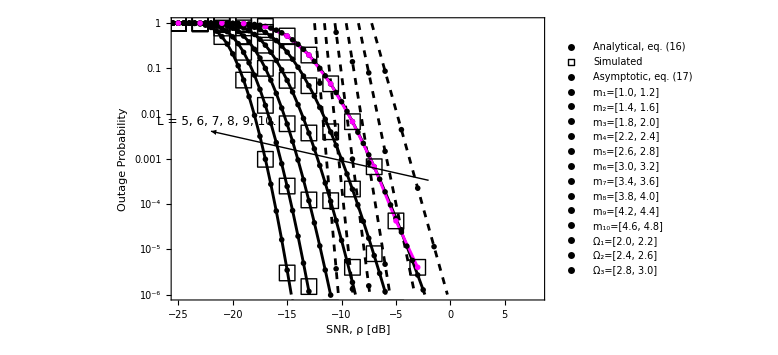

```mathematica
F1=ListLogPlot[{T1,T2,T3,T4,T5,T6,T1S,T2S,T3S,T4S,T5S,T6S,T1A,T2A,T3A,T4A,T5A,T6A},PlotStyle->{{Black,Thickness[0.0036]},{Black,Thickness[0.0036]},{Black,Thickness[0.0036]},{Black,Thickness[0.0036]},{Black,Thickness[0.0036]},{Black,Thickness[0.0036]},Black,Black,Black,Black,Black,Black,{Black,Dashed},{Black,Dashed},{Black,Dashed},{Black,Dashed},{Black,Dashed},{Black,Dashed},Magenta},Joined->{True,True,True,True,True,True,False,False,False,False,False,False,True,True,True,True,True,True},PlotMarkers->{{"",16},{"",16},{"",16},{"",16},{"",16},{"",16},{" □",16},{" □",16},{" □",16},{" □",16},{" □",16},{" □",16},{"",16},{"",16},{"",16},{"",16},{"",16},{"",16}},GridLines->Automatic,GridLinesStyle->Directive[White,Dashed,Thin],Frame-> True,FrameStyle->Directive[Black,18,FontFamily-> "Helvetica"],FrameLabel->{"SNR, ρ [dB]","Outage Probability"},ImageSize->Large,PlotRange->{{-25,8},{10^-6,1}},Axes->False,Epilog->{Text[Style["L = 5, 6, 7, 8, 9, 10.",12],{-21.5,-5}],{Arrowheads[Medium],Black,Arrow[{{-2,-8},{-22,-5.5}}]}},PlotLegends->{Placed[LineLegend[{Black,Black,Black},{"Analytical, eq. (16)","Simulated","Asymptotic, eq. (17)"},Joined->{False,False,False},LegendMarkers->{{"-",14},{"□",14},{"--",14}},LabelStyle->{Black,13,FontFamily-> "Helvetica"}],{0.15,0.12}],Placed[LineLegend[{Black,Black,Black,Black,Black,Black,Black,Black,Black,Black,Black},{"m_1=[1.0, 1.2]","m_2=[1.4, 1.6]","m_3=[1.8, 2.0]","m_4=[2.2, 2.4]","m_5=[2.6, 2.8]","m_6=[3.0, 3.2]","m_7=[3.4, 3.6]","m_8=[3.8, 4.0]","m_9=[4.2, 4.4]","m_10=[4.6, 4.8]"},Joined->{False,False,False,False,False,False,False,False,False,False},LegendMarkers->{{"",14},{"",16}},LabelStyle->{Black,11,FontFamily-> "Helvetica"}],{0.9,0.6}],Placed[LineLegend[{Black,Black,Black,Black,Black,Black,Black,Black,Black,Black,Black},{"Ω_1=[2.0, 2.2]","Ω_2=[2.4, 2.6]","Ω_3=[2.8, 3.0]","Ω_4=[3.2, 3.4]","Ω_5=[3.6, 3.8]","Ω_6=[4.0, 4.2]","Ω_7=[4.4, 4.6]","Ω_8=[4.8, 5.0]","Ω_9=[5.2, 5.4]","Ω_10=[5.6, 5.8]"},Joined->{False,False,False,False,False,False,False,False,False,False},LegendMarkers->{{"",14},{"",16}},LabelStyle->{Black,11,FontFamily-> "Helvetica"}],{0.75,0.6}]},FrameTicks->{{{{1,"1"},{0.1,"10^-1"},{0.01,"10^-2"},{10^-3,"10^-3"},{10^-4,"10^-4"},{10^-5,"10^-5"},{10^-6,"10^-6"}},None},{Automatic,None}}]
```